```mathematica
f1[xi_,xf_,τ_,t_]:=xi +(xf-xi)*(1-Exp[-t/τ])
s1[A_,σ_,ω_,ϕ_,t_]:=A*Exp[-σ*t]*Sin[ω*t+ϕ]
```

```mathematica
plot1[t_]:=f1[0.5,1,0.5,t]+s1[0.1,1.5,30,π/3,t]
plot2[t_]:=f1[0.85,1,0.5,t]+s1[0.1,1.5,20,π/2,t]
plot3[t_]:=f1[1.35,1.05,0.4,t]+s1[0.1,1.5,10,π/2,t]
```

```mathematica
plotOpts={AxesOrigin->{-0.1,0},Ticks->{{{0,Subscript[t, 0]},{1,Subscript[t, e]}},None},AxesStyle->Directive[Bold],AspectRatio->1,PlotRange->{{-0.1,1.1},Automatic} ,LabelStyle->Directive[24,Bold]}
```

{AxesOrigin→{-0.1,0},Ticks→{{{0,t_0},{1,t_e}},None},AxesStyle→Directive[Bold],AspectRatio→1,PlotRange→{{-0.1,1.1},Automatic},LabelStyle→Directive[14,Bold]}

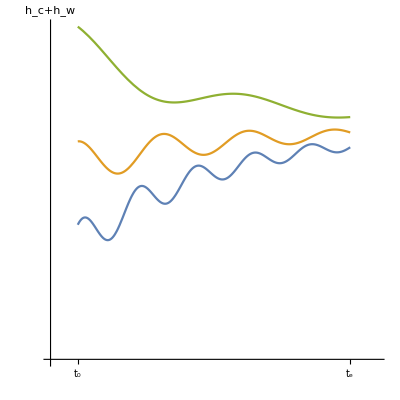

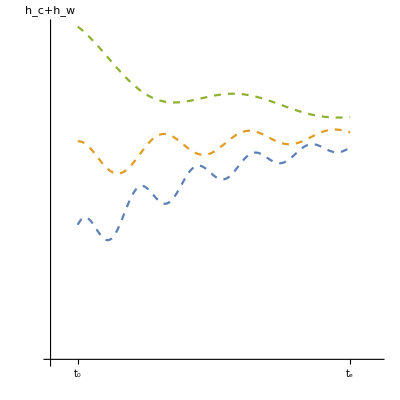

```mathematica
plot3lines=Plot[{plot1[t],plot2[t],plot3[t]},{t,0,1},AxesOrigin->{-0.1,0},Ticks->{{{0,Subscript[t, 0]},{1,Subscript[t, e]}},None},AxesStyle->Directive[Bold],AspectRatio->1,PlotRange->{{-0.1,1.1},Automatic} ,LabelStyle->Directive[24,Bold],AxesLabel->Subscript[h, w]+Subscript[h, c](*,Frame->{{True,False},{True,False}}, FrameLabel->{"",Subscript[h, w]+Subscript[h, c]}*)]
plot3linesDashed=Plot[{plot1[t],plot2[t],plot3[t]},{t,0,1},AxesOrigin->{-0.1,0},Ticks->{{{0,Subscript[t, 0]},{1,Subscript[t, e]}},None},AxesStyle->Directive[Bold],AspectRatio->1,PlotRange->{{-0.1,1.1},Automatic} ,LabelStyle->Directive[24,Bold],AxesLabel->Subscript[h, w]+Subscript[h, c],PlotStyle->Dashed(*,Frame->{{True,False},{True,False}}, FrameLabel->{"",Subscript[h, w]+Subscript[h, c]}*)]
```

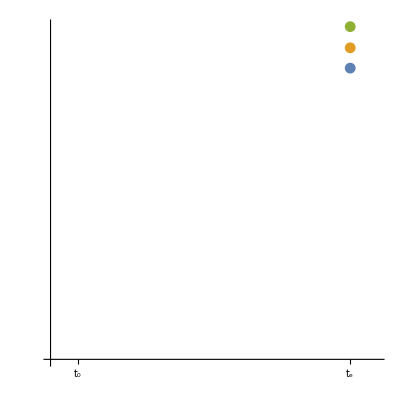

```mathematica
plot3dots=ListPlot[{{{t,plot1[t]}},{{t,plot2[t]}},{{t,plot3[t]}}}/.{t->1},plotOpts]
```

```mathematica
circlePlot=Graphics[{Red,Thick,Dashed,Opacity[0.25],Circle[{1,plot2[1]},{0.05,0.15}]}];
```

```mathematica
triSize=0.015;
triCenter={1,plot2[1]+0.025};
ℛ=Triangle[triSize {{Cos[30.Degree],-Sin[30.Degree]},{-Cos[30.Degree],-Sin[30.Degree]},{0,1}}+{triCenter,triCenter,triCenter}];
trianglePlot=Graphics[{Cyan,ℛ}];
```

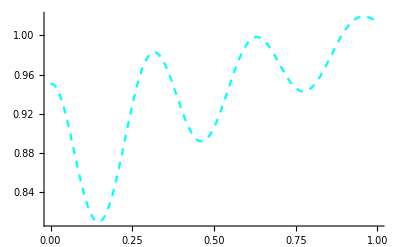

```mathematica
approachFun[A_,Δt_,T_,t_]:=A (1/2)^((T-t)/Δt)
approach1[t_]:=approachFun[0.025,0.1,1,t]
approachPlot=Plot[plot2[t]+approach1[t],{t,0,1},ColorFunction->Function[{x,y},Cyan],PlotStyle->Dashed]
```

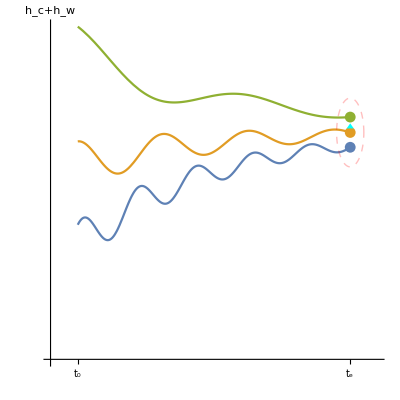

```mathematica
Show[plot3lines,plot3dots,circlePlot,trianglePlot]
```

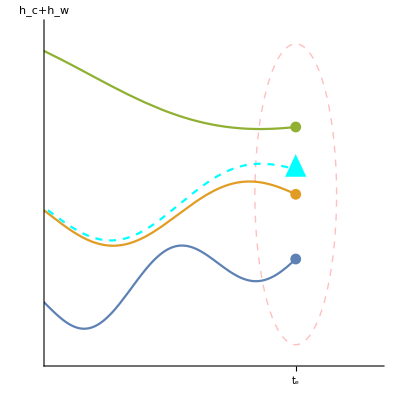

```mathematica
Show[plot3lines,plot3dots,circlePlot,trianglePlot,approachPlot, PlotRange->{{0.7,1.1},{-0.1+plot1[1],plot3[1]+0.1}},AspectRatio->1]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## Final Versions

### Wrist + Configuration Space

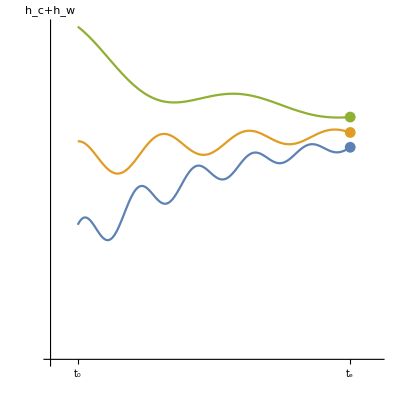

```mathematica
Show[plot3lines,plot3dots]
```

### “Basin of Attraction”

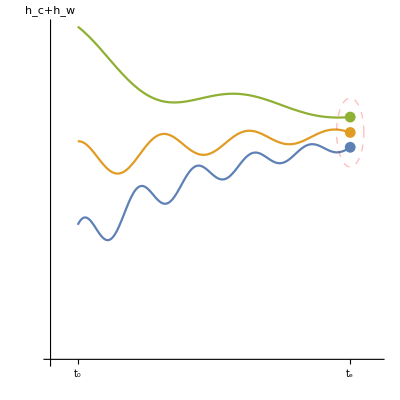

```mathematica
Show[plot3lines,plot3dots,circlePlot]
```

### Sampling in Equilibrium Configuration

```mathematica
Show[plot3lines,plot3dots,circlePlot,trianglePlot]
```

-Graphics-

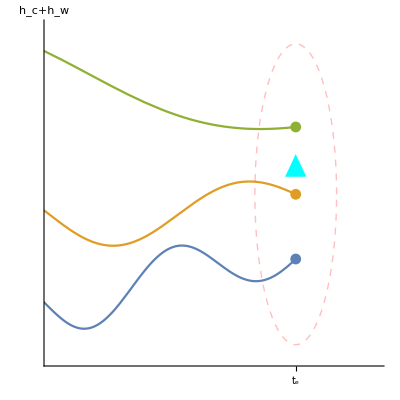

```mathematica
Show[plot3lines,plot3dots,circlePlot,trianglePlot, PlotRange->{{0.7,1.1},{-0.1+plot1[1],plot3[1]+0.1}},AspectRatio->1]
```

### Adapting

```mathematica
Show[plot3lines,plot3dots,circlePlot,trianglePlot,approachPlot,PlotRange->{{0.7,1.1},{-0.1+plot1[1],plot3[1]+0.1}},AspectRatio->1]
```

-Graphics-

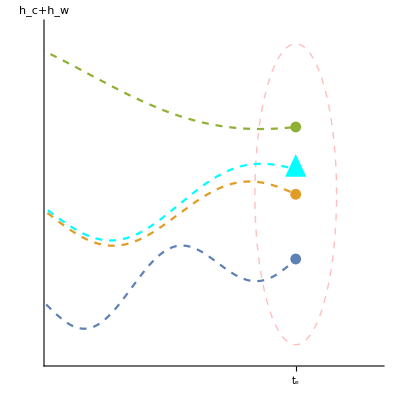

```mathematica
Show[plot3linesDashed,plot3dots,circlePlot,trianglePlot,approachPlot,PlotRange->{{0.7,1.1},{-0.1+plot1[1],plot3[1]+0.1}},AspectRatio->1]
```